```mathematica
n= 800 ;(*število naključnih točk*)
r=100;(*radij krožnice*)
```

```mathematica
Get["C:\\Users\\Uporabnik\\OneDrive - Univerza v Ljubljani\\Gal faks\\3.letnik\\1.semester\\Napredna računalniška orodja\\2.DN\\Funkcije.m"]
```

```mathematica
Matrika=Transpose[{RandomInteger[{-r,r},n],RandomInteger[{-100,100},n]}];
{Mat1,Mat2}=Module[{Matvn={},Matnot={}},
For[i=1,i<n,i++,
x=Matrika[[i]][[1]];
y=Matrika[[i]][[2]];
If[x^2+y^2<r^2,
AppendTo[Matnot,{x,y}],
AppendTo[Matvn,{x,y}]]];
{Matnot,Matvn}];
πapr=aproksimirajpi[Mat1,n]
```

3.135

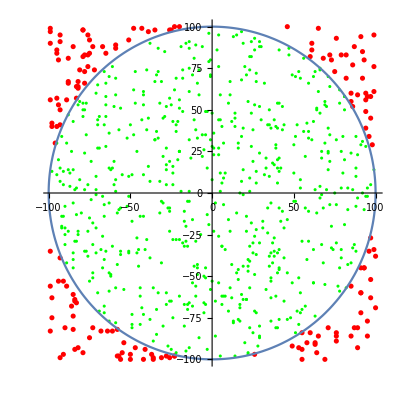

```mathematica
vn=ListPlot[Mat2,PlotStyle->Red];
not=ListPlot[Mat1,PlotStyle->Green];
c=ParametricPlot[{r*Cos[ϕ],r*Sin[ϕ]},{ϕ,0,2π}];
Show[{vn,not,c},AspectRatio->Automatic]
```

```mathematica
Clear[f,n,t,x]
```

```mathematica
izrisi[ft_]:=Module[{f=ft},
d=Series[f,{t,t0,4}];
p2=Plot[f,{t,0,4},PlotStyle->Red,PlotLegends->{"Točna funkcija"}];
Manipulate[
Show[
{Plot[Evaluate[Normal[Series[f,{t,t0,n}]]],{t,0,4},PlotStyle->Blue,PlotLegends->{"Približek"}],p2},
PlotRange->Automatic
],
{n,1,10,1}]];
```

```mathematica
t0=2;
izrisi[Sin[t]*t^2*Exp[-t]]
```